```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]⟦2;;-1,All⟧
]
```

## Plotting help

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{data,IDtheta},

IDtheta = {5,7,8};

(*convert data into a format which is read by Interpolation*)
Do[data[jj] = Table[{solution⟦ii,1⟧,solution⟦ii,jj+1⟧},{ii,1,Length[solution]}],{jj,1,Length[solution⟦1⟧]-1}];

Do[data[jj] = DeleteDuplicatesBy[data[jj],First],{jj,1,Length[solution⟦1⟧]-1}];

Do[data[jj] =Interpolation[data[jj],InterpolationOrder->1],{jj,1,Length[solution⟦1⟧]-1}];

Table[data[jj],{jj,Length[solution⟦1⟧]-1}]
]
```

### Plot Contour

```mathematica
PlotContour[data_,domain_,ratio_,range_]:=Module[{label},

label={Style["x",FontSize->14],Style["y",FontSize->14],None,None};

ContourPlot[data,{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],ContourLines->False,Contours->10,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/ratio,ContourLabels->False,Frame->True,FrameTicksStyle->{16,16},FrameLabel->label,RotateLabel->False,Exclusions->None]

]
```

### Plot Streamlines

```mathematica
PlotStreamlines[data_,domain_,ratio_,range_]:=Module[{},
StreamPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},PlotLegends->None,AspectRatio->1/ratio,StreamStyle->Green,StreamPoints->{Automatic,0.05},ImageSize->Large]]
```

### Plot Vector

```mathematica
PlotVectorlines[data_,domain_,ratio_,range_]:=Module[{},
VectorPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},ColorFunction->Hue,PlotLegends->Automatic,AspectRatio->1/ratio,VectorPoints->30,ImageSize->Large,VectorScale->0.05]]
```

### Sort Solution

## Heat Conduction

```mathematica
Clear[solution]
```

### M=3

```mathematica
ndof=5120;
foldername = "Tests/build/output_N6_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[3]= InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_5120

### M=4

```mathematica
ndof=8192;
foldername = "Tests/build/output_N9_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[4] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N9_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_8192

### M=5

```mathematica
ndof=14336;
foldername = "Tests/build/output_N12_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[5] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_14336

### M=6

```mathematica
ndof=20480;
foldername = "Tests/build/output_N16_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[6] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N16_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_20480

### M=7

```mathematica
ndof=30720;
foldername = "Tests/build/output_N20_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[7] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N20_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_30720

### M=8

```mathematica
ndof=40960;
foldername = "Tests/build/output_N25_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[8] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N25_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_40960

### M=9

```mathematica
ndof=56320;
foldername = "Tests/build/output_N30_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[9] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N30_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_56320

### M=10

```mathematica
ndof=71680;
foldername = "Tests/build/output_N36_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[10] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N36_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_71680

### M=11

```mathematica
ndof=93184;
foldername = "Tests/build/output_N42_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[11] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N42_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_93184

### M=12

```mathematica
ndof=114688;
foldername = "Tests/build/output_N49_poisson_heat_2D_Trun_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
solution[12] = InterpolateSolution[numsol];
```

Reading Data from...

../Tests/build/output_N49_poisson_heat_2D_Trun_Kn0p1/solution/numerical_solution_global_degree_1_DOF_114688

### error computation

```mathematica
errorθ=√2 Quiet[Table[Sqrt[NIntegrate[((√2)/3(solution[ii]⟦4⟧[x]+solution[ii]⟦6⟧[x]+solution[ii]⟦7⟧[x])-θExactHCKn0p1[x])^2,{x,0,0.5}]],{ii,3,12}]];
```

```mathematica
errorθ
```

{0.010541,0.010541,0.00618759,0.00618759,0.00392381,0.00392381,0.00273774,0.00273774,0.00210667,0.00210667}

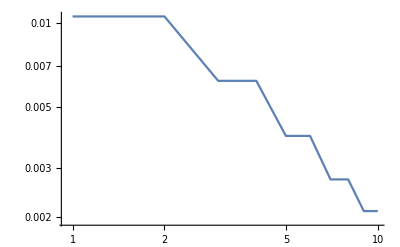

```mathematica
ListLogLogPlot[errorθ⟦1;;-1⟧,Joined->True]
```

### Temperature

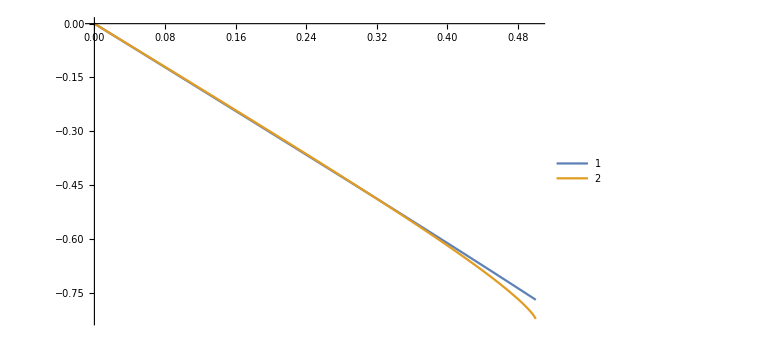

```mathematica
Plot[{(√2)/3(solution[3]⟦4⟧[x]+solution[3]⟦6⟧[x]+solution[3]⟦7⟧[x])(*,(√2)/3(solution[4]⟦1⟧[x]+solution[4]⟦2⟧[x]+solution[4]⟦3⟧[x]),(√2)/3(solution[5]⟦1⟧[x]+solution[5]⟦2⟧[x]+solution[5]⟦3⟧[x]),(√2)/3(solution[6]⟦1⟧[x]+solution[6]⟦2⟧[x]+solution[6]⟦3⟧[x])*),θExactHCKn0p1[x]},{x,0,0.5},PlotLegends->Automatic,ImageSize->Large]
```

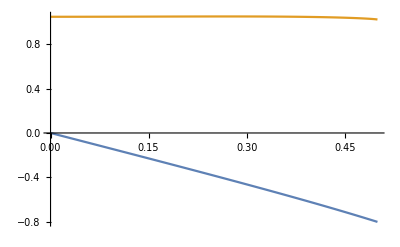

```mathematica
Plot[{(√2)/3(solution[5]⟦1⟧[x]+solution[5]⟦2⟧[x]+solution[5]⟦3⟧[x]),θExactKn0p1[x]},{x,0,0.5}]
```

# Reference Solution

### Poisson Heat

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

### Heat Conduction

```mathematica
exactHCKn0p1 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p3 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p5 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
(*exactHCKn0p1⟦All,4⟧+=1;
exactHCKn0p3⟦All,4⟧+=1;
exactHCKn0p5⟦All,4⟧+=1;*)

θExactHCKn0p1=Interpolation[exactHCKn0p1⟦All,{1,4}⟧];
σExactHCKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,6}⟧];
qExacHCtKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,7}⟧];

θExactHCKn0p3=Interpolation[exactHCKn0p3⟦All,{1,4}⟧];
σExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,6}⟧];
qExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,7}⟧];

θExactHCKn0p5=Interpolation[exactHCKn0p5⟦All,{1,4}⟧];
σExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,6}⟧];
qExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,7}⟧];
```

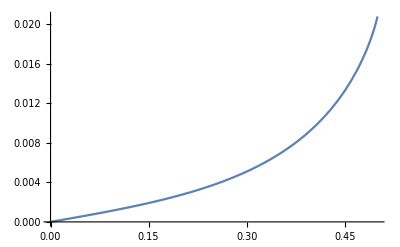

```mathematica
Plot[σExactHCKn0p1[x],{x,0,0.5}]
```